### Block entropy consistently approximates “biologicalness” across multiple block sizes

#### New correct result

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropy[ca, 3], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
ListStepPlot[Callout[#1, #2, Above,LabelVisibility->All]&@@@ReverseSortBy[entaps, First], LabelingSize->Large]]
```

-Graphics-

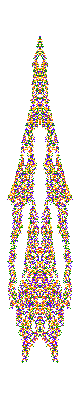
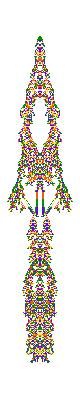
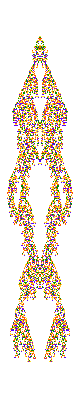
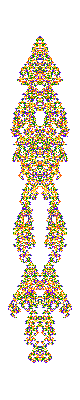
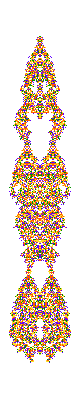
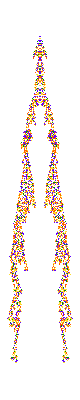
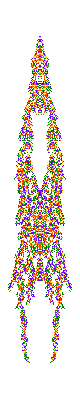
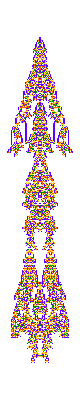
{-Graphics-9.35548,-Graphics-9.07966,-Graphics-9.00847,-Graphics-9.00479,-Graphics-8.91153,-Graphics-8.85666,-Graphics-8.8121,-Graphics-8.79664,-Graphics-8.75747,-Graphics-8.75147,-Graphics-8.73874,-Graphics-8.72291,-Graphics-8.71964,-Graphics-8.71572,-Graphics-8.65172,-Graphics-8.55526,-Graphics-8.53129,-Graphics-8.51178,-Graphics-8.47199,-Graphics-8.4701,-Graphics-8.39548,-Graphics-8.33038,-Graphics-8.31361,-Graphics-8.13241,-Graphics-8.11373,-Graphics-8.06022,-Graphics-7.91535,-Graphics-7.86596,-Graphics-7.81722,-Graphics-7.79934,-Graphics-7.76345,-Graphics-7.71557,-Graphics-7.6912,-Graphics-7.57353,-Graphics-7.49499,-Graphics-7.26193,-Graphics-7.1293,-Graphics-6.99851}

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropy[ca, 3], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
Labeled[#2, Style[Text[ToString[#1]], 10]]&@@@ReverseSortBy[entaps, First]]
```

All block sizes entropy distribution

```mathematica
With[{viable = Select[k5evos, #[[2]]>100&]},ListPlot3D[Catenate[MapIndexed[Append[Reverse[#2], #1]&, 
Table[Sort[PatchEntropy[CellularAutomaton[#[[1]], {{1}, 0},1000], size]&/@viable] , {size,2,10}], {2}]], AxesLabel->{"rank", "blocksize", "entropy"}]]
```

-Graphics3D-

#### All sorted by entropy across multiple blocksizes

```mathematica
ParallelTable[With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropy[ca, i], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
Labeled[GraphicsGrid[Partition[ReverseSortBy[entaps, First][[All, 2]], UpTo[10]], Frame->True], Text["blocksize: "<>ToString[i]]]], {i, {2, 3, 4, 5, 10, 20}}]
```

{-Graphics-blocksize: 2,-Graphics-blocksize: 3,-Graphics-blocksize: 4,-Graphics-blocksize: 5,-Graphics-blocksize: 10,-Graphics-blocksize: 20}

#### Old wrong result

Note: we were calculating entropy wrong before which is why we were getting weird results

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropyNZ[ca, 3], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
ListStepPlot[Callout[#1, #2, Above,LabelVisibility->All]&@@@SortBy[entaps, First], LabelingSize->Large]]
```

-Graphics-

#### How do the block distributions actually look?

```mathematica
ListLinePlot[With[{cas = Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 1000],{i,{8, 16, 27}}]},
cs = Rest[Values[ReverseSort[Counts[Catenate[Partition[#, {3, 3}, {1, 1}]]]]]] / Count[#, x_/;x>0, {2}]&/@ cas;
zs  = PadRight[#, Max[Length/@ cs]]&/@ cs;
MapThread[Legended[#1,ArrayPlot[#2[[;;TestCALifetime[#2] + 1]], ColorRules->colorrules, ImageSize->{Automatic, 80}]]&,{zs, cas}]]]
```

-Graphics-

```mathematica
Column[Table[GraphicsRow[PatchFrequencyChart[#, {k, k}, {1, 1}, {2, 10}, "SequenceSize"->{15, 15}]&/@ Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 1000],{i,{8, 16, 27}}]], {k, 2, 10}]]
```

-Graphics-

#### How are the blocks distributed across space?

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}, n = 10},
With[{ca = CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 250]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{50, Automatic}]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[;;n]]]]]]
```

-Graphics-

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[27, 1]], {{1}, 0}, 1000]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{100, Automatic}, "HighlightColor"->Red]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[;;n]]]]]]
```

-Graphics-

```mathematica
Module[{blockspec = {10, 10},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[27, 1]], {{1}, 0}, 1000]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{100, Automatic}, "HighlightColor"->Red, ColorRules->Table[i->LightGray, {i, 4}]]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,blockspec, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[Array[0&, blockspec]]][[;;5]]]]]]
```

-Graphics-

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}, n = 5},
With[{ca = CellularAutomaton[k5evos[[16, 1]], {{1}, 0}, 1000]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{100, Automatic}, "HighlightColor"->Red, ColorRules->Table[i->LightGray, {i, 4}]]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[50;;53]]]]]]
```

-Graphics-